```mathematica
1/(D[1-(u1/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) u1^(2(z-θ+1))/uh^(2z-2θ)(1-(u1/uh)^(θ-z)),u1]/.{u1-> us})
```

1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)))

```mathematica
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
pu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
βpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu,β},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(D[1-(u1/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) u1^(2(z-θ+1))/uh^(2z-2θ)(1-(u1/uh)^(θ-z)),u1]/.{u1-> us});
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
```

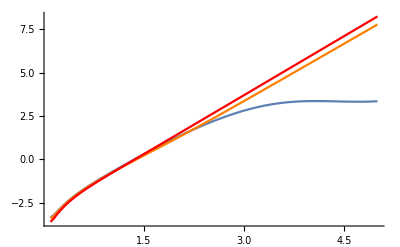

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.5389,1.0],1.5389,1.0]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.55,1.0],1.55,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.60,1.0],1.60,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

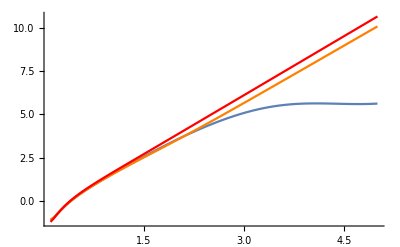

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[pu[i,10,0.1,1,0.75μextreme[1,1.5389,1.0],1.5389,1.0]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[pu[i,10,0.1,1,0.75μextreme[1,1.55,1.0],1.55,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[pu[i,10,0.1,1,0.75μextreme[1,1.60,1.0],1.60,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

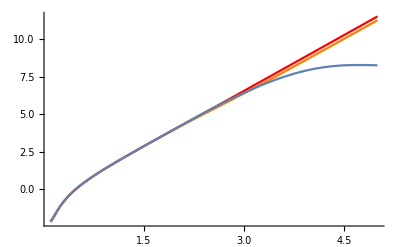

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1950],1.5,0.1950]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1991],1.5,0.1991]]//Log)},{i,0.1,5,0.05}]],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

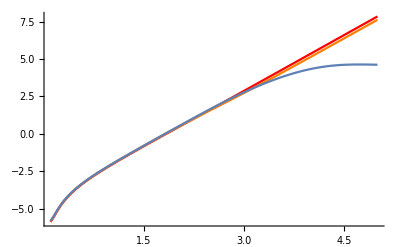

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1950],1.5,0.1950]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1991],1.5,0.1991]]//Log)},{i,0.1,5,0.05}]],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

```mathematica
Reduce[
q≤us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)))&&0<us≤uh&&uh>0&&0≤θ<2&&z≥1+θ/2&&μ≤Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]],{uh,us,μ,q,θ,z}]
```

$Aborted

```mathematica
Solve[
q==us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ))),z
]
```

$Aborted

```mathematica
Plot3D[qcrit[1,0.1,0.75μextreme[0.1,z,θ],z,θ]//Abs,{θ,0,2},{z,1,10},AxesLabel->{θ,z,qc}]
```

-Graphics3D-

1<=z<2 case

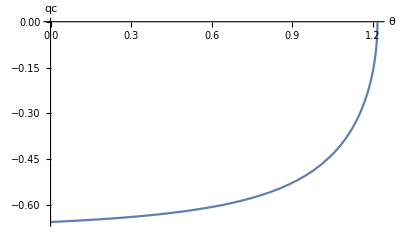

z>2 case

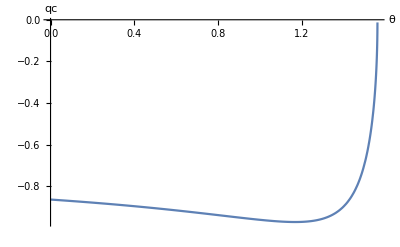

```mathematica
Print["1<=z<2 case"];
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,1.75,θ],1.75,θ],{θ,0,1.5},AxesLabel->{θ,qc},AxesOrigin->{0,0},PlotRange->All]];
Print["z>2 case"];
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,3,θ],3,θ],{θ,0,1.8},AxesLabel->{θ,qc},AxesOrigin->{0,0},PlotRange->All]];
```

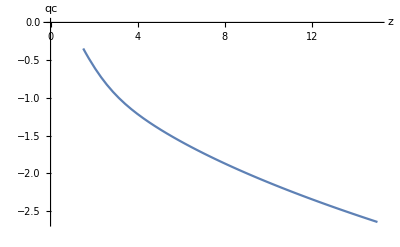

```mathematica
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,z,1],z,1],{z,1.5,15},AxesLabel->{z,qc},AxesOrigin->{0,0}]];
```

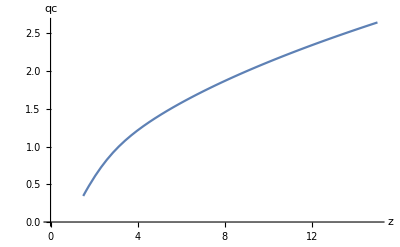

```mathematica
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,z,1],z,1]//Abs,{z,1.5,15},AxesLabel->{z,qc},AxesOrigin->{0,0}]];
```

1<=z<2 case

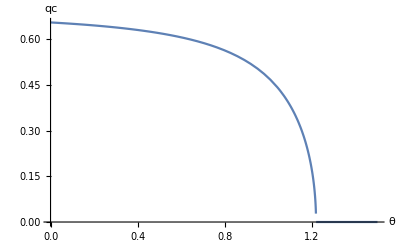

z>2 case

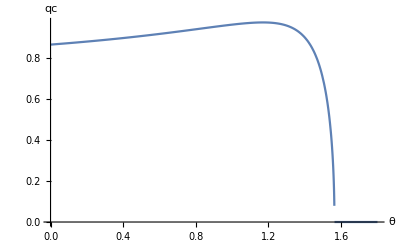

```mathematica
Print["1<=z<2 case"];
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,1.75,θ],1.75,θ]//Re//Abs,{θ,0,1.5},AxesLabel->{θ,qc},AxesOrigin->{0,0},PlotRange->All]];
Print["z>2 case"];
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,3,θ],3,θ]//Re//Abs,{θ,0,1.8},AxesLabel->{θ,qc},AxesOrigin->{0,0},PlotRange->All]];
```

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.5389,0.0],1.5389,0.0]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.55,0.0],1.55,0.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.60,0.0],1.60,0.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

$Aborted